## Lecture 11 : Matrix Algebra and Geometric Transformations

```mathematica
SetOptions[EvaluationNotebook[],ShowCellLabel->False];
```

```mathematica
SetOptions[{Plot,Plot3D,ContourPlot,ContourPlot3D, DensityPlot,ParametricPlot,ParametricPlot3D,ListPlot,ListLinePlot,ListPointPlot3D,Graphics,Graphics3D,PolarPlot}, ImageSize->Small,AxesLabel->{"x","y","z"}];
```

### Example 1 Rotate a point around Paround=(-5,-5) at the radius RR=3.5

```mathematica
RR1={0,3.5}; (*distance between 2 dots*)
```

```mathematica
Paround1={-5,-5}; (*red dots*)
```

```mathematica
(* Point1 {0,0} in the H-coordinates  *)
```

#### black dot with H coordinate

```mathematica
PointH1={0,0,1};
```

#### Rotation matrix

notice the use of composition!

```mathematica
RP1=Composition[TranslationTransform[Paround1],
RotationTransform[a],TranslationTransform[RR1]]
```

TransformationFunction[(1. Cos[a] | -1. Sin[a] | -5.-3.5 Sin[a]
1. Sin[a] | 1. Cos[a] | -5.+3.5 Cos[a]
0 | 0 | 1.)]

```mathematica
-Graphics-;
```

```mathematica
(* The order of transformations 
1) TranslationTransform[Paround1] 
2)RotationTransform[a] 
3)TranslationTransform[RR1]] *)
```

#### Transformation Matrix

```mathematica
MP1=TransformationMatrix[RP1] (*actionable - we've transformed the tranfromation function*)
```

{{1. Cos[a],-1. Sin[a],-5.-3.5 Sin[a]},{1. Sin[a],1. Cos[a],-5.+3.5 Cos[a]},{0,0,1.}}

```mathematica
MatrixForm[MP1]
```

(1. Cos[a] | -1. Sin[a] | -5.-3.5 Sin[a]
1. Sin[a] | 1. Cos[a] | -5.+3.5 Cos[a]
0 | 0 | 1.)

```mathematica
(* Evaluate converts the formula MP1 into a matrix-function of a MFP1[a] *)
```

```mathematica
MFP1[a_]:=Evaluate[MP1] (*obtain real function to be used*)
```

```mathematica
MatrixForm[MFP1[a]]
```

(1. Cos[a] | -1. Sin[a] | -5.-3.5 Sin[a]
1. Sin[a] | 1. Cos[a] | -5.+3.5 Cos[a]
0 | 0 | 1.)

```mathematica
(* Vector-function PR1[t] is the resulting vector in the H-coordinates,  where [[1;;2]] eliminates the H-component of PR1[t] (it is always =1)  *)
```

#### point H1 is the homogeneous vector of the point

the . is a matrix multiplication operation

matrix multiplication the matrix function with the homogeneous function

```mathematica
PR1[t_]:=(MFP1[t].PointH1)[[1(*start*);;2(*end at inclusive*)]] (*get rid of the last element*)
```

```mathematica
MFP1[t].PointH1
```

{-5.-3.5 Sin[t],-5.+3.5 Cos[t],1.}

```mathematica
MatrixForm[PR1[t]]
```

(-5.-3.5 Sin[t]
-5.+3.5 Cos[t])

```mathematica
(*  Example. i;;j selects a part of a list by index from i to j such as A[[i;;j]]  *)
```

```mathematica
{1,2,3,8,9,10}[[2;;4]]
```

{2,3,8}

```mathematica
(* The center of rotation is PParound1 (Red) *)
```

```mathematica
PParound1:={PointSize[0.05],Red,Point[Paround1]}
```

```mathematica
(* Animation by PR1[t] *)
```

```mathematica
AnimPR1[t_]:=
Graphics[
{{PointSize[0.05],Point[PR1[t] (*new position of black dot*)]},PParound1},
Axes->True,PlotRange->15]
```

```mathematica
Manipulate[{AnimPR1[t],PR1[t]},{t,0,2Pi}]
```

### (* Example 1 Rotate a point around Paround=(-5,-5) at the radius RR=3.5 *)

```mathematica
RR1={0,3.5};
```

```mathematica
Paround1={-5,-5};
```

```mathematica
(* Point1 {0,0} in the H-coordinates  *)
```

```mathematica
PointH1={0,0,1};
```

```mathematica
(* Getting the rotation matrix (3 steps)  *)
```

```mathematica
RP1=Composition[TranslationTransform[Paround1],RotationTransform[a],TranslationTransform[RR1]]
```

TransformationFunction[(1. Cos[a] | -1. Sin[a] | -5.-3.5 Sin[a]
1. Sin[a] | 1. Cos[a] | -5.+3.5 Cos[a]
0 | 0 | 1.)]

```mathematica
(* The odrer of transformations 1) TranslationTransform[Paround1] 2)RotationTransform[a] 3)TranslationTransform[RR1]] *)
```

```mathematica
MP1=TransformationMatrix[RP1]
```

{{1. Cos[a],-1. Sin[a],-5.-3.5 Sin[a]},{1. Sin[a],1. Cos[a],-5.+3.5 Cos[a]},{0,0,1.}}

```mathematica
(* Evaluate converts the formula MP1 into a matrix-function of a MFP1[a] *)
```

```mathematica
MFP1[a_]:=Evaluate[MP1]
```

```mathematica
MatrixForm[MFP1[a]]
```

(1. Cos[a] | -1. Sin[a] | -5.-3.5 Sin[a]
1. Sin[a] | 1. Cos[a] | -5.+3.5 Cos[a]
0 | 0 | 1.)

```mathematica
(* Vector-function PR1[t] is the resulting vector in the H-coordinates,  where [[1;;2]] eliminates the H-component of PR1[t] (it is always =1)  *)
```

```mathematica
PR1[t_]:=(MFP1[t].PointH1)[[1;;2]]
```

```mathematica
MatrixForm[PR1[t]]
```

(-5.-3.5 Sin[t]
-5.+3.5 Cos[t])

```mathematica
(*  Example. i;;j selects a part of a list by index from i to j such as A[[i;;j]]  *)
```

```mathematica
{1,2,3,8,9,10}[[2;;4]]
```

{2,3,8}

```mathematica
(* The center of rotation is PParound1 (Red) *)
```

```mathematica
PParound1:={PointSize[0.05],Red,Point[Paround1]}
```

```mathematica
(* Animation by PR1[t] *)
```

```mathematica
AnimPR1[t_]:=Graphics[{{PointSize[0.05],Point[PR1[t]]},PParound1},Axes->True,PlotRange->15]
```

```mathematica
Manipulate[{AnimPR1[t],PR1[t]},{t,0,2Pi}]
```

### (* Example 1' Back to the geometric transforms. Let us solve the same problem using primitives *)

```mathematica
RR1={0,3.5};
```

```mathematica
Paround1={-5,-5};
```

```mathematica
(* Point1 {0,0} no H-coordinates ! *)
```

```mathematica
myPoint={0,0};
```

```mathematica
(* The object - primitive, the function Point has been applied, but too early fo the wrapper Graphics *)
```

```mathematica
Object1={Black,PointSize[0.05],Point[myPoint]}
```

{GrayLevel[0],PointSize[0.05],Point[{0,0}]}

```mathematica
(* Transformation function: GeometricTransformation, Composition- composes the transformations*)
```

```mathematica
GT1[a_]:=GeometricTransformation[Object1,Composition[TranslationTransform[Paround1],RotationTransform[a],TranslationTransform[RR1]]]
```

```mathematica
(* Center of rotation *)
```

```mathematica
PParound1:={PointSize[0.05],Red,Point[Paround1]}
```

```mathematica
(* Animation by PR1[t] *)
```

```mathematica
myAnim1[t_]:=Graphics[{{PointSize[0.05],GT1[t]},PParound1},Axes->True,PlotRange->15]
```

```mathematica
Manipulate[myAnim1[t],{t,0,2Pi}]
```

### (* Example 2' Alternative solution by primitives and the transform RotationTransform[a,Paround1] (instead of TranslationTransform[Paround1],RotationTransform[a] *)

```mathematica
RR1={0,3.5};
```

```mathematica
Paround1={-5,-5};
```

```mathematica
(* The original position of the our point is Pinit1=Paround1+RR1 
Here the Translation has been replaced by addition of vectors *)
```

#### Translation replace by the addition of vectors

```mathematica
Pinit1=Paround1+RR1
```

{-5,-1.5}

```mathematica
Object2={Purple,PointSize[0.05],Point[Pinit1]}
```

{RGBColor[0.5, 0, 0.5],PointSize[0.05],Point[{-5,-1.5}]}

```mathematica
PParound1:={PointSize[0.05],Red,Point[Paround1]}
```

#### obtain transformation function

```mathematica
T2p[a_]:=GeometricTransformation[Object2,RotationTransform[a,Paround1]]
```

```mathematica
T2p[1]
```

GeometricTransformation[{RGBColor[0.5, 0, 0.5],PointSize[0.05],Point[{-5,-1.5}]},{{{Cos[1],-Sin[1]},{Sin[1],Cos[1]}},{5 (-1+Cos[1]-Sin[1]),5 (-1+Cos[1]+Sin[1])}}]

```mathematica
(* Let is Rotate this point around Paround using the rotation function Rotate[a,p] *)
```

```mathematica
(* PlotRange has been modified for the best animation range PlotRange->{{0,-15},{0,-15}} *)
```

```mathematica
myAnim2p[a_]:=Graphics[{T2p[a],PParound1},Axes->True,PlotRange->{{0,-15},{0,-15}}]
```

```mathematica
Manipulate[myAnim2p[a],{a,0,2Pi}]
```

```mathematica
(* Exercise 1: Solve problem 1 using Matrix Algebra by a single transform RotationTransform[a,Paround1] *)
```

### (*Example 3 Rotate a vector object f[x_]:=x^2 for x={-1,1} around the origin using Matric Algebra *)

```mathematica
f2[x_]:=x^2
```

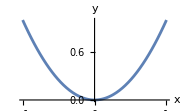

```mathematica
Plot[f2[t],{t,-1,1}]
```

```mathematica
RT2=RotationTransform[a]
```

TransformationFunction[(Cos[a] | -Sin[a] | 0
Sin[a] | Cos[a] | 0
0 | 0 | 1)]

```mathematica
(* Rotation around the origin  *)
```

```mathematica
M2=TransformationMatrix[RT2]
```

{{Cos[a],-Sin[a],0},{Sin[a],Cos[a],0},{0,0,1}}

#### Convert the formula into the matrix-function

```mathematica
M2F[a_]:=Evaluate[M2]
```

#### Convert the explicit function y=f[x] into the parametric form in the H- coordinates

```mathematica
S2H[t_]:={t, f2[t],1}
```

```mathematica
S2H[s]
```

{s,s^2,1}

```mathematica
(* Rotate and cut the H coordinate using ;; *)
```

```mathematica
PR2[a_,t_]:=(M2F[a].S2H[t])[[1;;2]]
```

```mathematica
MatrixForm[PR2[a,t]]
```

(t Cos[a]-t^2 Sin[a]
t^2 Cos[a]+t Sin[a])

```mathematica
(* Plot of the the rotated curve *)
```

```mathematica
p2[a_]:=ParametricPlot[PR2[a,t],{t,-1,1},PlotRange->1]
```

#### Zero

```mathematica
(*  Zero *)
```

```mathematica
Zero={Red,PointSize[0.05],Point[{0,0}]}
```

{RGBColor[1, 0, 0],PointSize[0.05],Point[{0,0}]}

```mathematica
Zero2=Graphics[Zero];
```

#### Animate

```mathematica
(*  Animate *)
```

```mathematica
p2All[t_]:=Show[p2[t],Zero2]
```

```mathematica
Manipulate[p2All[a],{a,0,2Pi}]
```

1. matrix rotation
2. explicit -> parametric equation (matrix)

### Example 4 Rotate a parametric curve 2{Sin[2t],Cos[3t]} around the point Paround5={5/2,5/2} with the angular speed a at the radius R5=3/2. Additionally rotate the curve around itself (center) with the angular speed b. Use the primitive S5P

```mathematica
Paround5={5/2,5/2}; (*point to rotate around*)
```

```mathematica
RR5={0,3/2};
```

```mathematica
S5[t_]:=2{Sin[2t],Cos[3t]}
```

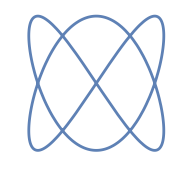

```mathematica
S5G=ParametricPlot[S5[t],{t,0,2Pi}, Axes->False] (*not primitive*)
```

#### geometric transformation uses primitive -> convert param plot to primitive

```mathematica
(* Convert the graphics into the primitive, immediate assignment "=", important! S5P becomes a collection of primitives,
Show S5P without ;  *)
```

```mathematica
S5P=S5G[[1]];
```

```mathematica
(* Check *)
```

```mathematica
Graphics[S5P]
```

-Graphics-

```mathematica
(* The object to be rotated *)
```

```mathematica
Zero={Red,PointSize[0.05],Point[{0,0}]}
```

{RGBColor[1, 0, 0],PointSize[0.05],Point[{0,0}]}

```mathematica
Object5={Zero,S5P};
```

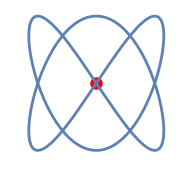

```mathematica
Graphics[Object5]
```

```mathematica
RT5[a_,b_]:=GeometricTransformation[Object5 , 
Composition[
RotationTransform[a,Paround5](*rotate around the purple point*) ,TranslationTransform[RR5], (*RR5 distance between the dots*)
RotationTransform[b]]] (*rotate arount it self -> b, since no point specify*)
;
```

```mathematica
GParound5={Purple,PointSize[0.05],Point[Paround5]};
```

```mathematica
ShowAll5[a_,b_]:=Graphics[{RT5[a,b],GParound5},PlotRange->7,Axes->True]
```

```mathematica
Manipulate[ShowAll5[a,b],{a,0,2Pi},{b,0,2Pi}]
```

```mathematica
(* To speed up a=b. Planets motion analogy ! *)
```

```mathematica
Manipulate[ShowAll5[a,a],{a,0,2Pi}]
```

## Basic 2 and 3D Transformations

```mathematica
-Graphics-;
```

```mathematica
-Graphics-;
```

no argumer -> default {0,0}

### geometric transformation only works for primitive!

```mathematica
(* The last 2 functions will be explained later *)
```

### Example 1 Graphics3D Primitives. Rotate a Torus[{x,y,z},R1,R2] positioned at {0,0,0} around the y-axis : vector {0,1,0} and around a vector (0,0,1) anchored at {1,1,0}

#### object definition

```mathematica
R1=1;R2=2;
```

```mathematica
Tor={Purple,Opacity[0.5],Torus[{0,0,0} (*where*),{R1,R2} (*{inner, outer}*)]};
```

```mathematica
Zero3={Red,PointSize[0.06],Point[{0,0,0}]};
```

#### Rotate around the Y-axis

```mathematica
Yrot=2{0,1,0};
```

```mathematica
ArY={Thick,Green,Arrow[{{0,0,0},Yrot}]} (*point arrow in the y direction*)
```

{Thickness[Large],RGBColor[0, 1, 0],Arrow[{{0,0,0},{0,2,0}}]}

```mathematica
AllTor={Tor,Zero3,ArY}
```

{{RGBColor[0.5, 0, 0.5],Opacity[0.5],Torus[{0,0,0},{1,2}]},{RGBColor[1, 0, 0],PointSize[0.06],Point[{0,0,0}]},{Thickness[Large],RGBColor[0, 1, 0],Arrow[{{0,0,0},{0,2,0}}]}}

```mathematica
(*Check  *)
```

```mathematica
Graphics3D[AllTor,Axes->True, Boxed->True]
```

-Graphics3D-

#### rotate AllTor about Yrot with angle a

```mathematica
Rot1Tor[a_]:=GeometricTransformation[AllTor,RotationTransform[a,Yrot] (*RotationTransform[a,w vector non zero vector]*)]
```

```mathematica
(*Check  *)
```

```mathematica
Graphics3D[Rot1Tor[Pi/2]]
```

-Graphics3D-

#### rotate object around the green arrow/axis

```mathematica
Manipulate[Graphics3D[Rot1Tor[a],PlotRange->2,Axes->True],{a,0,12Pi}]
```

### Rotation around and around a vector Zrot=(0,0,1) ancored at Anc={2,2,0}

#### object definition

```mathematica
Zrot=3{0,0,1};
```

```mathematica
An={2,2,0};
```

```mathematica
ArZ={Thick,Red,Arrow[{An,An+Zrot}]};
```

```mathematica
AllTorZ={Tor,Zero3,ArZ};
```

```mathematica
AllTor2={Tor,Zero3};
```

```mathematica
(* Check  *)
```

```mathematica
Graphics3D[{AllTor2,ArZ},Axes->True,Boxed->True]
```

-Graphics3D-

#### rotate AllTor around ZRot, which is anchored at point An

```mathematica
Rot2Tor[a_]:=GeometricTransformation[AllTor2,RotationTransform[a,Zrot,An]]
```

```mathematica
Manipulate[Graphics3D[{Zero3,ArZ,Rot2Tor[a]},PlotRange->{{-3,7},{-3,7},{-2,3}},Axes->True],{a,0,12Pi}]
```

### (* Exercise Additionally rotate the Torus around its center in the Y direction *)

```mathematica
Rot3Tor[a_]:=GeometricTransformation[AllTor2,
Composition[RotationTransform[a,Zrot,An], (*rotate AllTor around ZRot, which is anchored at point An*)
 RotationTransform[6a,Yrot] (*then also rotate it around the y axis, which is anchor at itself*)
]]
```

```mathematica
Manipulate[Graphics3D[{Zero3,ArZ,Rot3Tor[a]},PlotRange->{{-3,7},{-3,7},{-5,5}},Axes->True],{a,0,2Pi}]
```